## Dynamics of the model with differentiation

### Include cell differentiation where reproduction happens in the next compartment

The model tracks the movement of the cells from compartments X_n → X_(n-1)→ X_(n-2)→ . . . → X_0
All cells in compartment X_0 are off cells which all others are on
The switch from X_0→X_n occurs with probability μ

In this notebook we extend the model to include differentiation. Thus each cell can thus undergo four processes:

1. Differentiation
	x_i→ x_(i-1)+x_(i-1) with probability ϵ
2. Death
	x_i→ϕ with probability d
3. Switch to X_n
	x_i→x_n with probability μ (valid only for i = 0 and μ = 0 otherwise)
4. Reproduce
	x_i→ x_i+x_i with probability (1-ϵ-d-μ)

As compared to the main text now we represent the rates with probabilities of each process to materialise. 
Thus the interpretation of the rates changes but the essence of the model stays the same.
The deterministic dynamics of the process can then be described by the following three equations:

OverDot[x_n]= x_n(1-2 ϵ-2 d)+μ x_0
OverDot[x_i]= x_i(1- 2 ϵ - 2 d) +2 ϵ x_(i+1) (for i = 1,...,n-1)
OverDot[x_0] = x_0(1-2 d- 2 μ) +2 ϵ x_(n-1)

### Running the model for three cycles, each lasting for 100 time-steps.

The plots below show the population size in the on and off compartments for different leaching rates (rows) and different memory sizes (5,15,25,35). This corresponds to the main text figure Transient dynamics in multi-state memory (b).

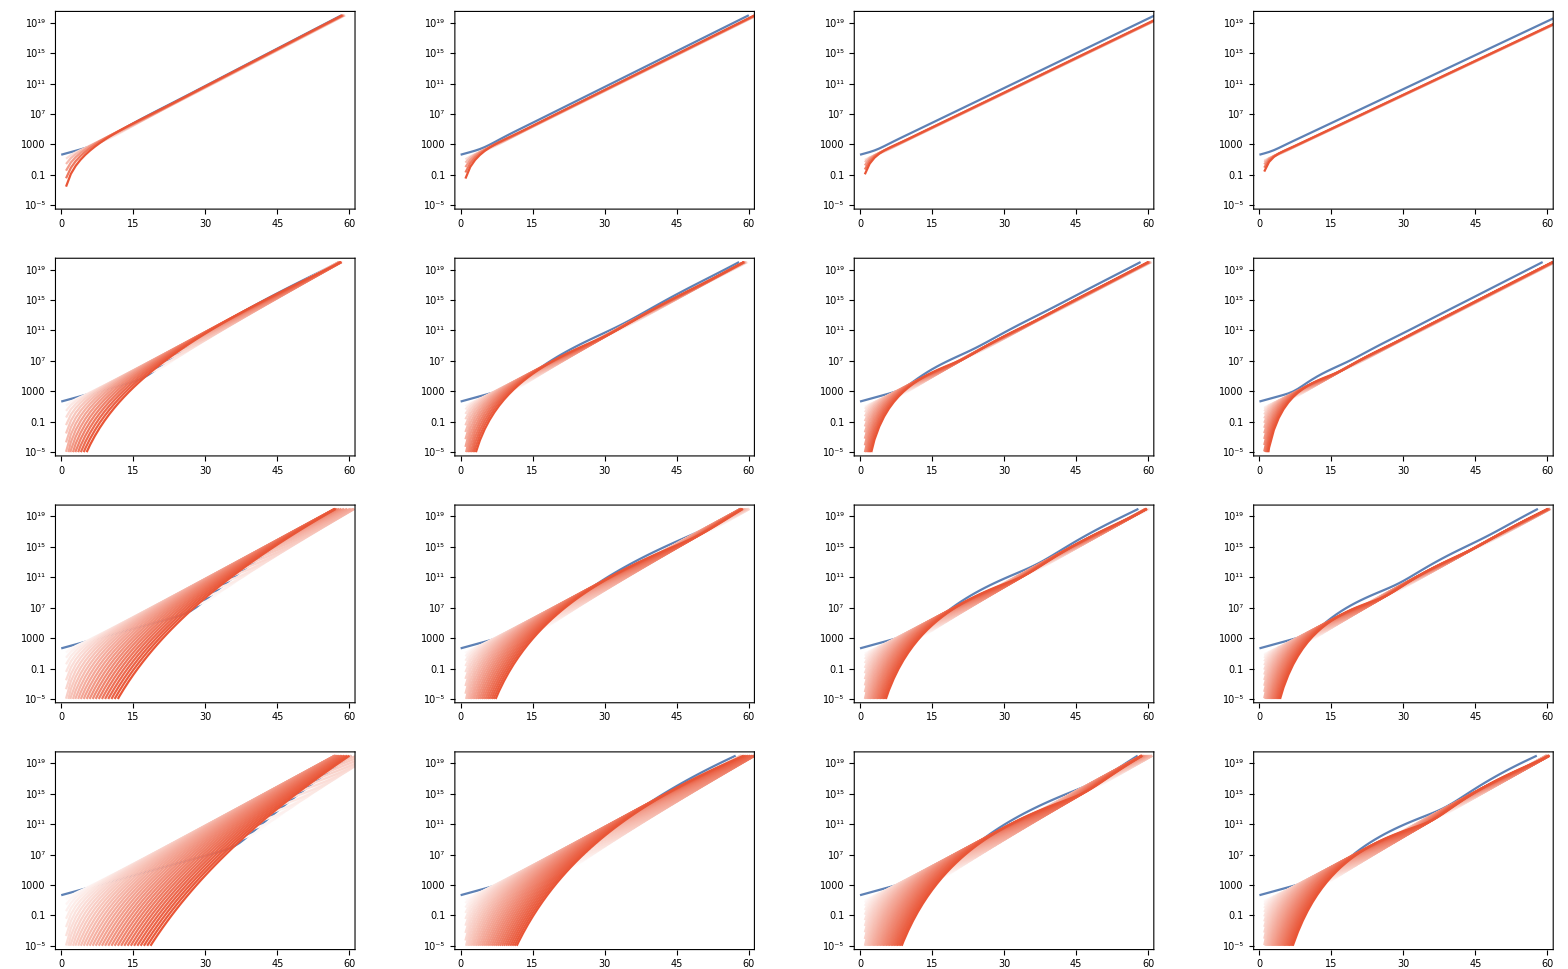

```mathematica
newscheme={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.915, 0.3325, 0.2125]};
ClearAll;
graphs={};
onlyfrequencies={};
Table[{
initialfrequencies=Join[{45},ConstantArray[0,imax-1]];
d=0.1;
ϵ=leach;
tmax=100;
(*dilution=5;*)
biglist={};
maxcycles=3;
initfinalpopsizes={};
For[cycle=1,cycle≤maxcycles,cycle++,
μ=0.2;
offequation=(1-2 d-2μ)Subscript[x, 0][t]+2 ϵ Subscript[x, imax-1][t];
fullonequation=(1-2 ϵ-2 d)Subscript[x, 1][t]+μ Subscript[x, 0][t];
generalform[i_]:=(1-2 ϵ-2 d)Subscript[x, i][t]+2 ϵ Subscript[x, i-1][t];
lhs=Table[Subscript[x, i]'[t],{i,0,imax-1}];
rhs=If[imax==2,Flatten[{offequation,fullonequation}],Flatten[{offequation,fullonequation,Table[generalform[i],{i,2,imax-1}]}]];
(*timelist={};*)
sol[μ_]:=NDSolve[Join[Table[lhs⟦i⟧==rhs⟦i⟧,{i,1,imax}],Table[Subscript[x, i][0]==initialfrequencies⟦i+1⟧,{i,0,imax-1}]],Table[Subscript[x, i],{i,0,imax-1}],{t,0,tmax},PrecisionGoal->Automatic];
toappend=Flatten[Table[Evaluate[Table[Subscript[x, i][t],{i,0,imax-1}]/.sol[μ]],{t,0,tmax}],1];
AppendTo[initfinalpopsizes,{toappend⟦1⟧//Total,toappend⟦-2⟧//Total}];
initialfrequencies=toappend⟦-1⟧;
AppendTo[biglist,Drop[toappend,-1]];
];
flatlist=Flatten[biglist,1];
frequencies=#/Total[#]&/@flatlist;
offlist=frequencies⟦All,1⟧;
onlist=Table[∑_(i=2)^imax frequencies⟦j,i⟧,{j,1,Length[frequencies]}];
AppendTo[onlyfrequencies,onlist];
AppendTo[graphs,{GeometricMean[Table[1/(tmax -1)(Log[initfinalpopsizes⟦i,2⟧]-Log[initfinalpopsizes⟦i,1⟧]),{i,1,maxcycles,1}]],(Log[flatlist⟦-1⟧//Total]-Log[flatlist⟦1⟧//Total])/(maxcycles tmax -1)//N,ListLogPlot[Table[flatlist⟦All,i⟧,{i,1,imax}],Joined->True,PlotStyle->Flatten[{newscheme⟦1⟧,Lighter[newscheme⟦15⟧,#]&/@Table[1-1/(imax-1) i,{i,1,imax-1}]}],DataRange->{0,tmax maxcycles},PlotRange->{{0,60},{10^-5,10^20}},GridLines->{Table[tmax cycle+1,{cycle,1,maxcycles}], None},(*PlotLegends->Table[i,{i,0,imax-1}],*)Frame->True,FrameStyle->Directive[Black,Thickness[0.004]]],ListPlot[Table[frequencies⟦All,i⟧,{i,1,imax}],Joined->True,PlotStyle->Flatten[{newscheme⟦1⟧,Lighter[newscheme⟦15⟧,#]&/@Table[1-1/(imax-1) i,{i,1,imax-1}]}],DataRange->{0,tmax maxcycles},PlotRange->{{0,60},Automatic},GridLines->{Table[tmax cycle+1,{cycle,1,maxcycles}], None},PlotLegends->Table[i,{i,0,imax-1}],Frame->True],
ListPlot[{offlist,onlist(*,onlist PeakDetect[onlist,0,0,0.001+Last[onlist]]*)},Joined->{True, True, False},Filling->{3->0},FillingStyle->Opacity[1],PlotStyle->Append[newscheme⟦{1,-1}⟧,Black],PlotRange->{{0,60},Full},DataRange->{0,tmax maxcycles},GridLines->{Table[tmax cycle+1,{cycle,1,maxcycles}]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]]],Last[flatlist],Last[flatlist]//Total}]},{imax,{6,16,26,36}},{leach,{0.2,0.4,0.6,0.8}}];
GraphicsGrid[Partition[graphs⟦All,3⟧,4]]
```

### Transient dynamics for different number of compartments

The plots show the increase in over(under) shoots as the number of compartments is increased from 5, 15, 25, 35

```mathematica
sublists=Partition[onlyfrequencies,4];
leachs={0.2,0.4,0.6,0.8};
place={{{50,0.5},{100,0.25},{200,0.2},{250,0.11}},{{50,0.9},{100,0.68},{200,0.53},{250,0.42}},{{250,0.95},{150,0.9},{200,0.8},{250,0.7}},{{250,0.95},{150,0.9},{200,0.8},{250,0.7}}};
tabs=Table[ListPlot[Table[Callout[sublists⟦j⟧⟦i⟧,"ϵ = "<>ToString[leachs⟦i⟧],place⟦j⟧⟦i⟧,LabelStyle->Directive[14,Black],CalloutStyle->Black],{i,1,4,1}],Joined->True,PlotStyle->newscheme,(*PlotStyle->newscheme⟦4⟧,*)PlotRange->{{-10,310},{-0.05,1.05}},DataRange->{0,tmax maxcycles},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Frequency of on cells",14,Black]},ImagePadding->All],{j,1,Length[sublists],1}];
GraphicsGrid[Partition[tabs,2]]
```

-Graphics-

### Transient dynamics of multi-state memory for a given ϵ

Focus on only the first cycle which runs for 100 time steps.

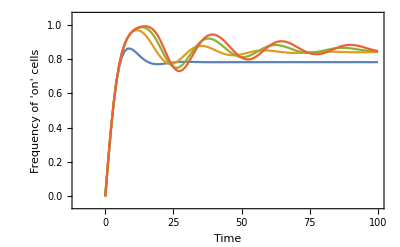

```mathematica
ListPlot[onlyfrequencies⟦{1,6,11,16},1;;100⟧,Joined->True,(*PlotStyle->newscheme⟦4⟧,*)PlotRange->{{-10,100},{-0.05,1.05}},DataRange->{0,tmax},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Frequency of 'on' cells",14,Black]}]
```